```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
numRAD=7;
epsi=1;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["./tmp.dat","Table"]
```

{{#,L[fm^-1],C_0[nucl]},{4,-505.15},{6,-741.15},{8,-974.604},{10,-1206.79}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2 b2+4 lam))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
CalcDimerE[basisW_,lam_,lec_]:=
Module[{eval,evec},
Nd=Length[basisW];
hamm=Table[ham[lam,basisW[[i]],basisW[[j]],lec],{i,Nd},{j,Nd}];
normm=Table[norm[basisW[[i]],basisW[[j]]],{i,Nd},{j,Nd}];
{eval,evec}=Eigensystem[{hamm,normm}];
ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];
{eigsorted[[1]],Transpose[{vecsorted[[1]],basisW}]}
];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_,σw_:2]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
Print[LECc];
widths={};
rndPrec=5;
Do[

widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];

(*t1=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmin,σw],{Ns,IntegerPart[Nd/2]}]];
t2=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmax,σw],{Ns,IntegerPart[Nd/2]}]];

widthLr=ArrayReshape[Flatten[#]&/@Tuples[{t1,t2}],{Nd,Ns}];*)

widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];

AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[(
(eigsorted[[1]]<results)&&
(eigsorted[[1]]>-2.65)&&
(Im[eigsorted[[1]]]==0)&&
(NormTF[Transpose[{vecsorted[[1]],wi}]]>10^-5)&&
(Min[Abs[vecsorted[[1]]]]>10^-2)&&
(ContainsOnly[Sign[vecsorted[[1]]],{1}]||ContainsOnly[Sign[vecsorted[[1]]],{-1}])
),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (1/2^(7/2)) (Pi/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];


VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2=(π^(3/2)/4) Cc/(lam Bb + Aa(lam + 2Gg +2  Bb) + lam Hh +2 Bb Hh+Gg(lam +2Hh))^(3/2);
w2= 2lam(Aa+Hh)(Gg+Bb)/(lam Bb + Aa(lam+2 Gg+2Bb)+lam Hh +2 Bb Hh+Gg(lam+2Hh));
eta3 =(π^(3/2)/4) Cc/(lam Bb + Gg(lam + 2Bb)+lam Hh +2Bb Hh + Aa(lam+2Gg+2Hh))^(3/2);
w3 = 2lam(Aa+Bb)(Gg+Hh)/(lam Bb + Gg(lam+2Bb)+lam Hh +2Bb Hh+Aa(lam+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq,radMA},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3,Sinh1,Sinh2,Sinh3,CoshA,numRAD=radMA},
zeta1=-(π^(3/2)/(√2))/(Aa+Bb+Gg+ Hh)^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta3=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

(*SinhA=If[((b1!=0.0)&&(Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Sinh[b1 r rp]/b1,0.0];
SinhB=If[((b2!=0.0)&&(Abs[b2 r rp]<0.1 Abs[a2 r^2+c2 rp^2])&&(Abs[a2 r^2+c2 rp^2]<numRAD)),Exp[-a2 r^2-c2 rp^2] Sinh[b2 r rp]/b2,0.0];
SinhC=If[((b3!=0.0)&&(Abs[b3 r rp]<0.1 Abs[a3 r^2+c3 rp^2])&&(Abs[a3 r^2+c3 rp^2]<numRAD)),Exp[-a3 r^2-c3 rp^2] Sinh[b3 r rp]/b3,0.0];
CoshA=If[((Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Cosh[b1 r rp],0.0];*)
Sinh1=(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1+100 $MachineEpsilon);
Sinh2=(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2+100 $MachineEpsilon);
Sinh3=(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3+100 $MachineEpsilon);

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)

(*SinhA=If[b1==0.0,0.0,(Exp[-a1 r^2-c1 rp^2+b1 r rp]-Exp[-a1 r^2-c1 rp^2-b1 r rp])/(2 b1)];
SinhB=If[b2==0.0,0.0,(Exp[-a2 r^2-c2 rp^2+b2 r rp]-Exp[-a2 r^2-c2 rp^2-b2 r rp])/(2 b2)];
SinhC=If[b3==0.0,0.0,(Exp[-a3 r^2-c3 rp^2+b3 r rp]-Exp[-a3 r^2-c3 rp^2-b3 r rp])/(2 b3)];
CoshA=0.5 (Exp[-a1 r^2-c1 rp^2+b1 r rp]+Exp[-a1 r^2-c1 rp^2+b1 r rp]);*)

(*-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) SinhA-4 a1 Sqrt[3]^-1 (-r rp CoshA+SinhB))+zeta2 SinhB+zeta3 SinhC)*)
(*Chop[Exp[-a3 r^2-c3 rp^2] SinhC,10^-10]*)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ,numR_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq,numR],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; 

AppendTo[Wmats,cij (amat+wmat)];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins"];
tanDelta
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001,numR_]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
(*TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
TanDelSwave*)
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2,numR];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39850  in 4 parallel threads.

Core 2 : -1.86791{{0.155946,0.13312},{0.418562,0.93926},{0.856897,5.9105},{0.257322,16.169}}

Core 3 : -1.71432{{0.110568,0.066369},{0.444434,0.92933},{0.850148,5.6687},{0.259812,26.71}}

Core 4 : -1.85795{{0.172418,0.12065},{0.498011,1.2155},{0.788573,6.0061},{0.316874,18.04}}

Core 1 : -1.77403{{0.157202,0.10564},{0.512272,1.0947},{0.214865,6.1184},{0.816516,7.5417}}

optimum of 39850 candidate width sets found in Δt = 7.102811 sec.          : E_0 = -1.86791

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39873  in 4 parallel threads.

Core 1 : -1.64779{{-0.0797925,0.070033},{-0.305032,0.45806},{-0.899074,4.6396},{-0.303735,21.925}}

Core 2 : -2.03884{{-0.105305,0.072086},{-0.372411,0.68569},{-0.757741,4.0149},{-0.525405,14.962}}

Core 3 : -1.853{{-0.0946739,0.055149},{-0.364698,0.6844},{-0.651525,3.3228},{-0.658443,13.581}}

Core 4 : -1.49208{{0.228525,0.19783},{0.575513,1.8659},{0.784475,9.2427},{0.0340408,16.97}}

optimum of 39873 candidate width sets found in Δt = 7.224693 sec.          : E_0 = -2.03884

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39827  in 4 parallel threads.

Core 3 : -2.05244{{-0.113518,0.076938},{-0.345169,0.7016},{-0.563085,3.0373},{-0.742231,11.081}}

Core 4 : -1.72906{{0.169583,0.15978},{0.419973,1.0731},{0.87941,6.7599},{0.146638,21.635}}

Core 1 : -1.82368{{0.179114,0.13719},{0.479862,1.2825},{0.828044,6.4382},{0.228021,24.614}}

Core 2 : -1.96493{{-0.0939864,0.059156},{-0.379853,0.66833},{-0.75283,3.9768},{-0.529269,15.052}}

optimum of 39827 candidate width sets found in Δt = 7.233843 sec.          : E_0 = -2.05244

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39755  in 4 parallel threads.

Core 2 : -2.09019{{-0.0920879,0.080121},{-0.185378,0.43021},{-0.473614,1.775},{-0.856064,9.0739}}

Core 3 : -1.91634{{0.107724,0.069722},{0.429089,0.71686},{0.79451,4.9452},{0.415971,12.129}}

Core 4 : -1.90338{{-0.0725757,0.075901},{-0.212949,0.32246},{-0.687005,2.5175},{-0.690949,12.54}}

Core 1 : -1.97485{{-0.101986,0.087657},{-0.139114,0.44001},{-0.370731,1.3094},{-0.912581,7.2503}}

optimum of 39755 candidate width sets found in Δt = 7.196332 sec.          : E_0 = -2.09019

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39812  in 4 parallel threads.

Core 2 : -1.84193{{-0.113084,0.066128},{-0.397026,0.81663},{-0.426439,2.9762},{-0.804818,9.8418}}

Core 3 : -2.15849{{-0.0666261,0.06019},{-0.22022,0.34828},{-0.542784,2.0822},{-0.807744,9.3124}}

Core 4 : -1.91051{{-0.163444,0.13643},{-0.244344,0.7856},{-0.511915,2.4749},{-0.807171,10.512}}

Core 1 : -1.89239{{0.171142,0.11938},{0.482529,0.96068},{0.611929,5.034},{0.602843,9.4794}}

optimum of 39812 candidate width sets found in Δt = 7.22836 sec.          : E_0 = -2.15849

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39819  in 4 parallel threads.

Core 2 : -1.76352{{-0.13903,0.08305},{-0.420391,0.95799},{-0.691051,4.037},{-0.571305,16.138}}

Core 1 : -1.98128{{0.163527,0.11583},{0.419396,0.9715},{0.658706,4.1697},{0.602886,13.066}}

Core 3 : -1.85658{{-0.0747069,0.053846},{-0.32398,0.40807},{-0.661263,3.2276},{-0.672448,8.8692}}

Core 4 : -1.79701{{0.103265,0.072719},{0.366189,0.51674},{0.621498,3.6398},{0.684823,8.0973}}

optimum of 39819 candidate width sets found in Δt = 7.134811 sec.          : E_0 = -1.98128

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39737  in 4 parallel threads.

Core 2 : -1.97838{{-0.0992317,0.075815},{-0.198934,0.53098},{-0.429349,1.6989},{-0.87535,9.0948}}

Core 3 : -1.87989{{0.157511,0.1144},{0.488957,1.1187},{0.824448,6.4761},{0.237481,15.982}}

Core 4 : -1.84772{{-0.0568286,0.034879},{-0.339958,0.4135},{-0.684626,3.3037},{-0.642251,9.8655}}

Core 1 : -2.03882{{-0.0995249,0.083815},{-0.306082,0.53349},{-0.77573,3.6262},{-0.542818,14.679}}

optimum of 39737 candidate width sets found in Δt = 7.056478 sec.          : E_0 = -2.03882

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39857  in 4 parallel threads.

Core 1 : -1.78052{{0.153384,0.10972},{0.417127,1.0574},{0.843778,5.3247},{0.300862,29.243}}

Core 2 : -1.78952{{0.159708,0.14095},{0.432741,1.0306},{0.873542,6.6944},{0.155412,17.037}}

Core 3 : -1.84586{{-0.141439,0.12915},{-0.313121,0.71233},{-0.83804,4.2955},{-0.423839,19.668}}

Core 4 : -1.98445{{0.141409,0.094466},{0.451194,0.9214},{0.741053,4.8581},{0.476726,13.737}}

optimum of 39857 candidate width sets found in Δt = 7.275071 sec.          : E_0 = -1.98445

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39803  in 4 parallel threads.

Core 3 : -1.98903{{0.13354,0.11097},{0.359852,0.76238},{0.8317,4.635},{0.401185,18.123}}

Core 1 : -1.90732{{0.162346,0.13271},{0.435459,1.0737},{0.851396,6.0613},{0.243198,21.926}}

Core 2 : -1.94548{{0.145781,0.12248},{0.394889,0.89171},{0.857264,5.4423},{0.296495,20.057}}

Core 4 : -1.97204{{0.115789,0.09599},{0.348791,0.6873},{0.855631,4.6701},{0.364463,20.227}}

optimum of 39803 candidate width sets found in Δt = 7.076974 sec.          : E_0 = -1.98903

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39778  in 4 parallel threads.

Core 2 : -2.02588{{-0.0439799,0.035963},{-0.251059,0.29836},{-0.647051,2.4926},{-0.718582,10.505}}

Core 4 : -1.95012{{-0.05978,0.047041},{-0.216303,0.32761},{-0.368776,1.5707},{-0.902022,6.4827}}

Core 1 : -1.95183{{0.165904,0.13306},{0.411604,0.97028},{0.802676,5.0788},{0.398459,16.483}}

Core 3 : -1.92851{{0.115937,0.077504},{0.437913,0.79581},{0.819795,5.3251},{0.350323,13.787}}

optimum of 39778 candidate width sets found in Δt = 7.110483 sec.          : E_0 = -2.02588

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39672  in 4 parallel threads.

Core 1 : -2.07759{{-0.117007,0.095681},{-0.261946,0.58256},{-0.434985,2.2507},{-0.853511,8.3617}}

Core 2 : -2.03549{{-0.131655,0.1047},{-0.259794,0.67373},{-0.510275,2.4245},{-0.809193,10.311}}

Core 3 : -2.04438{{-0.0233281,0.021506},{-0.191728,0.20782},{-0.514039,1.6594},{-0.83574,8.5371}}

Core 4 : -2.05986{{-0.0953662,0.062402},{-0.362357,0.62545},{-0.644043,3.4006},{-0.666942,11.539}}

optimum of 39672 candidate width sets found in Δt = 7.051254 sec.          : E_0 = -2.07759

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39861  in 4 parallel threads.

Core 1 : -1.84207{{-0.0978797,0.086722},{-0.32224,0.55703},{-0.879985,4.6365},{-0.334975,20.495}}

Core 2 : -1.57693{{-0.0981402,0.089571},{-0.273155,0.48762},{-0.88145,4.0258},{-0.372561,27.649}}

Core 3 : -1.79472{{0.160746,0.14991},{0.37624,0.88593},{0.866848,5.511},{0.284919,18.658}}

Core 4 : -1.88737{{0.167923,0.11599},{0.477778,0.98641},{0.431359,4.545},{0.746633,8.6074}}

optimum of 39861 candidate width sets found in Δt = 7.187799 sec.          : E_0 = -1.88737

-741.15

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39808  in 4 parallel threads.

Core 1 : -1.83279{{0.16077,0.10542},{0.515502,0.98667},{0.7208,6.024},{0.434578,9.2648}}

Core 2 : -1.79089{{0.13412,0.093216},{0.460838,0.85391},{0.835403,6.1128},{0.267847,9.6191}}

Core 3 : -2.03236{{-0.140817,0.12031},{-0.294083,0.6623},{-0.628672,3.126},{-0.706015,11.204}}

Core 4 : -1.9217{{0.181362,0.14776},{0.377546,0.92029},{0.677199,4.1068},{0.604953,12.258}}

optimum of 39808 candidate width sets found in Δt = 7.183136 sec.          : E_0 = -2.03236

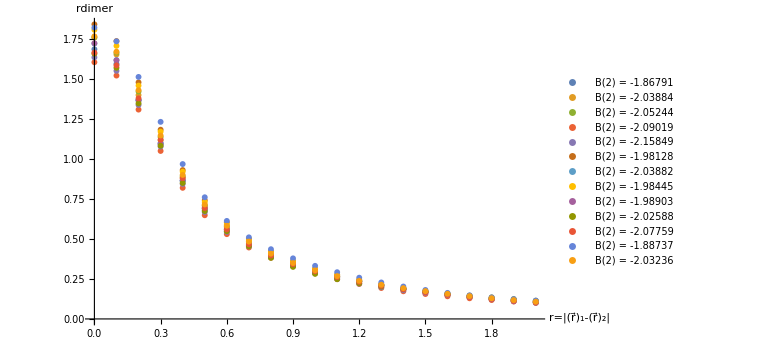

```mathematica
flag=1;

lambdaTest=6;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
dCores={};
(*WS={4.3584650 ,  2.8802200 ,  2.0651530  , 1.6563710  , 1.1615310  , 0.8261400,0.5922700  , 0.4901080 ,  0.3227900   ,0.2522220  , 0.1357500};
dCores={CalcDimerE[WS,lambdaTest,LECc]}*)

ncc=13;
If[flag>0,
Do[
{eDi,wDi}=ApproxDimerWF[lambdaTest,4,4,10000,0.001,Random[Real,{15,35}],0.01,1,2];
AppendTo[dCores,{eDi,wDi}];
,{nc,Range[ncc]}];
];

If[flag>=0,
NormTF[#]&/@dCores[[All,2]];

dCores=CalcDimerE[dCores[[#]][[2]][[All,2]],lambdaTest,LECc]&/@Range[Length[dCores]];

JacobiTrailWavefunctionU=Total[Abs[#[[1]]] Exp[-#[[2]] r1^2]&/@#[[2]]]&/@dCores;rR=Range[0,2,0.100];
JacobiTrailWavefunctionDataU=Table[#/.{r1->R1},{R1,rR}]&/@JacobiTrailWavefunctionU;

plotData=Transpose[{rR,#}]&/@JacobiTrailWavefunctionDataU;

lgd="B(2) = "<>ToString[#[[1]]]&/@dCores;
ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large]
]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.001;
(* Integration grid *)
rMa=12;
grdPerFermi=10;
nGrd=IntegerPart[rMa grdPerFermi];
results={};
(*dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];*)
nbrOfCores=Length[dCores];

Do[
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ,numRAD];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print["core ",nn,"| maxE=",numRAD," )  λ=",lambdaTest," ; C_0(λ)=",LECc," ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; B(2)=",e0Core," ; dim_d=",dimCore," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbar/√(Mm Abs[e0Core]))];
,{nn,Length[dCores]},{numRAD,{1}}];
```

finite-difference runtime Δt = 0.327057 mins

core 1| maxE=1 )  λ=6 ; C_0(λ)=-741.15 ; R_max=12 ; #=120 ; E_match=0.001 ; B(2)=-1.86791 ; dim_d=4 ; a_dd=2.95565 ; a_dd/a_aa=0.627256

finite-difference runtime Δt = 0.335051 mins

core 2| maxE=1 )  λ=6 ; C_0(λ)=-741.15 ; R_max=12 ; #=120 ; E_match=0.001 ; B(2)=-2.03884 ; dim_d=4 ; a_dd=3.62012 ; a_dd/a_aa=0.802652

finite-difference runtime Δt = 0.349084 mins

core 3| maxE=1 )  λ=6 ; C_0(λ)=-741.15 ; R_max=12 ; #=120 ; E_match=0.001 ; B(2)=-2.05244 ; dim_d=4 ; a_dd=3.61502 ; a_dd/a_aa=0.804191

finite-difference runtime Δt = 0.353 mins

core 4| maxE=1 )  λ=6 ; C_0(λ)=-741.15 ; R_max=12 ; #=120 ; E_match=0.001 ; B(2)=-2.09019 ; dim_d=4 ; a_dd=3.05006 ; a_dd/a_aa=0.684723

finite-difference runtime Δt = 0.351956 mins

core 5| maxE=1 )  λ=6 ; C_0(λ)=-741.15 ; R_max=12 ; #=120 ; E_match=0.001 ; B(2)=-2.15849 ; dim_d=4 ; a_dd=1.55065 ; a_dd/a_aa=0.353754

finite-difference runtime Δt = 0.354856 mins

core 6| maxE=1 )  λ=6 ; C_0(λ)=-741.15 ; R_max=12 ; #=120 ; E_match=0.001 ; B(2)=-1.98128 ; dim_d=4 ; a_dd=3.28505 ; a_dd/a_aa=0.718005

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

finite-difference runtime Δt = 0.0804007 mins

core 4| maxE=31 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = 1.54153 fm        a_dd/a_aa = 0.342823

finite-difference runtime Δt = 0.0822169 mins

core 4| maxE=33 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = 1.31031 fm        a_dd/a_aa = 0.291402

finite-difference runtime Δt = 0.0836343 mins

core 4| maxE=35 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = 1.05665 fm        a_dd/a_aa = 0.234991

finite-difference runtime Δt = 0.0828675 mins

core 4| maxE=37 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = 0.796147 fm        a_dd/a_aa = 0.177057

finite-difference runtime Δt = 0.0833759 mins

core 4| maxE=39 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = 0.553986 fm        a_dd/a_aa = 0.123202

finite-difference runtime Δt = 0.0863583 mins

core 4| maxE=41 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = 0.300927 fm        a_dd/a_aa = 0.0669239

finite-difference runtime Δt = 0.0837157 mins

core 4| maxE=43 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = 0.0329207 fm        a_dd/a_aa = 0.0073213

finite-difference runtime Δt = 0.0846511 mins

core 4| maxE=45 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = -0.243845 fm        a_dd/a_aa = -0.0542291

finite-difference runtime Δt = 0.0850437 mins

core 4| maxE=47 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = -0.526965 fm        a_dd/a_aa = -0.117193

finite-difference runtime Δt = 0.085938 mins

core 4| maxE=49 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = -0.800102 fm        a_dd/a_aa = -0.177936

finite-difference runtime Δt = 0.086226 mins

core 4| maxE=51 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = -1.102 fm        a_dd/a_aa = -0.245076

finite-difference runtime Δt = 0.0866551 mins

core 4| maxE=53 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = -1.38369 fm        a_dd/a_aa = -0.307722

finite-difference runtime Δt = 0.0863025 mins

core 4| maxE=55 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = -1.61073 fm        a_dd/a_aa = -0.358213

finite-difference runtime Δt = 0.0855587 mins

core 4| maxE=57 )  λ = 6   C_0(λ) = -1090.55     R_max = 5     #(grid points) = 75                a_dd = -1.83058 fm        a_dd/a_aa = -0.407106

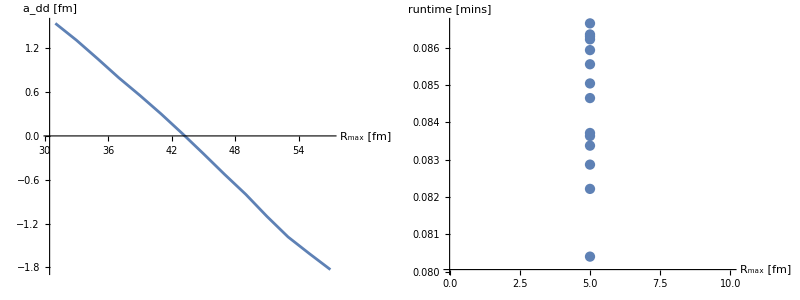

```mathematica
rMaxStart=31;
rMaxEnd=58;
nbrR=2;

coreNBR=4;
{e0Core,dimerCore}=dCores[[coreNBR]];

RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
RmaxRange=Range[rMaxStart,rMaxEnd,nbrR];
energ=0.001;
grdPerFermi=15;
numRAD=9;
results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
rMa=5;
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ,numRAD];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["core ",coreNBR,"| maxE=",numRAD," )  λ = ",lambdaTest,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{numRAD,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

```mathematica
Table[Exp[-x] Sinh[x 0.3],{x,Range[115.1,1111]}]
```

{5.10345×10^-36,2.5343×10^-36,1.25849×10^-36,6.2495×10^-37,3.10341×10^-37,1.54111×10^-37,7.65291×10^-38,3.80032×10^-38,1.88719×10^-38,9.37148×10^-39,4.65374×10^-39,2.31098×10^-39,1.1476×10^-39,5.69881×10^-40,2.82994×10^-40,1.40531×10^-40,6.97855×10^-41,3.46545×10^-41,1.72089×10^-41,8.54569×10^-42,4.24366×10^-42,2.10734×10^-42,1.04647×10^-42,5.19664×10^-43,2.58057×10^-43,1.28148×10^-43,6.36362×10^-44,3.16008×10^-44,1.56925×10^-44,7.79266×10^-45,3.86972×10^-45,1.92165×10^-45,9.54261×10^-46,4.73872×10^-46,2.35318×10^-46,1.16855×10^-46,5.80287×10^-47,2.88162×10^-47,1.43097×10^-47,7.10598×10^-48,3.52873×10^-48,1.75231×10^-48,8.70173×10^-49,4.32115×10^-49,2.14582×10^-49,1.06558×10^-49,5.29153×10^-50,2.6277×10^-50,1.30488×10^-50,6.47982×10^-51,3.21778×10^-51,1.5979×10^-51,7.93495×10^-52,3.94038×10^-52,1.95674×10^-52,9.71686×10^-53,4.82525×10^-53,2.39615×10^-53,1.18989×10^-53,5.90883×10^-54,2.93424×10^-54,1.4571×10^-54,7.23574×10^-55,3.59316×10^-55,1.78431×10^-55,8.86063×10^-56,4.40006×10^-56,2.185×10^-56,1.08504×10^-56,5.38816×10^-57,2.67568×10^-57,1.3287×10^-57,6.59814×10^-58,3.27654×10^-58,1.62708×10^-58,8.07985×10^-59,4.01233×10^-59,1.99247×10^-59,9.8943×10^-60,4.91336×10^-60,2.4399×10^-60,1.21162×10^-60,6.01673×10^-61,2.98782×10^-61,1.48371×10^-61,7.36787×10^-62,3.65878×10^-62,1.81689×10^-62,9.02243×10^-63,4.48041×10^-63,2.2249×10^-63,1.10485×10^-63,5.48655×10^-64,2.72454×10^-64,1.35297×10^-64,6.71863×10^-65,3.33637×10^-65,1.65679×10^-65,8.22739×10^-66,4.0856×10^-66,2.02885×10^-66,1.0075×10^-66,5.00308×10^-67,2.48446×10^-67,1.23374×10^-67,6.1266×10^-68,3.04238×10^-68,1.5108×10^-68,7.50241×10^-69,3.72559×10^-69,1.85007×10^-69,9.18718×10^-70,4.56222×10^-70,2.26553×10^-70,1.12503×10^-70,5.58673×10^-71,2.77429×10^-71,1.37767×10^-71,6.84131×10^-72,3.39729×10^-72,1.68705×10^-72,8.37763×10^-73,4.16021×10^-73,2.0659×10^-73,1.02589×10^-73,5.09444×10^-74,2.52982×10^-74,1.25627×10^-74,6.23847×10^-75,3.09793×10^-75,1.53839×10^-75,7.63941×10^-76,3.79362×10^-76,1.88385×10^-76,9.35494×10^-77,4.64553×10^-77,2.3069×10^-77,1.14557×10^-77,5.68875×10^-78,2.82495×10^-78,1.40283×10^-78,6.96624×10^-79,3.45933×10^-79,1.71785×10^-79,8.5306×10^-80,4.23617×10^-80,2.10362×10^-80,1.04463×10^-80,5.18747×10^-81,2.57602×10^-81,1.27921×10^-81,6.35239×10^-82,3.1545×10^-82,1.56648×10^-82,7.7789×10^-83,3.86289×10^-83,1.91825×10^-83,9.52577×10^-84,4.73036×10^-84,2.34903×10^-84,1.16649×10^-84,5.79263×10^-85,2.87653×10^-85,1.42844×10^-85,7.09344×10^-86,3.5225×10^-86,1.74922×10^-86,8.68638×10^-87,4.31353×10^-87,2.14203×10^-87,1.0637×10^-87,5.28219×10^-88,2.62306×10^-88,1.30257×10^-88,6.46838×10^-89,3.2121×10^-89,1.59508×10^-89,7.92095×10^-90,3.93343×10^-90,1.95328×10^-90,9.69971×10^-91,4.81673×10^-91,2.39192×10^-91,1.18779×10^-91,5.8984×10^-92,2.92906×10^-92,1.45453×10^-92,7.22297×10^-93,3.58682×10^-93,1.78116×10^-93,8.84499×10^-94,4.39229×10^-94,2.18115×10^-94,1.08313×10^-94,5.37865×10^-95,2.67096×10^-95,1.32636×10^-95,6.5865×10^-96,3.27076×10^-96,1.62421×10^-96,8.06559×10^-97,4.00525×10^-97,1.98895×10^-97,9.87683×10^-98,4.90469×10^-98,2.4356×10^-98,1.20948×10^-98,6.00611×10^-99,2.98255×10^-99,1.48109×10^-99,7.35487×10^-100,3.65232×10^-100,1.81369×10^-100,9.00651×10^-101,4.4725×10^-101,2.22098×10^-101,1.1029×10^-101,5.47686×10^-102,2.71973×10^-102,1.35058×10^-102,6.70677×10^-103,3.33048×10^-103,1.65387×10^-103,8.21287×10^-104,4.07839×10^-104,2.02527×10^-104,1.00572×10^-104,4.99425×10^-105,2.48007×10^-105,1.23157×10^-105,6.11578×10^-106,3.03701×10^-106,1.50813×10^-106,7.48917×10^-107,3.71901×10^-107,1.84681×10^-107,9.17097×10^-108,4.55417×10^-108,2.26153×10^-108,1.12304×10^-108,5.57687×10^-109,2.76939×10^-109,1.37524×10^-109,6.82924×10^-110,3.3913×10^-110,1.68407×10^-110,8.36284×10^-111,4.15286×10^-111,2.06225×10^-111,1.02408×10^-111,5.08545×10^-112,2.52536×10^-112,1.25406×10^-112,6.22746×10^-113,3.09246×10^-113,1.53567×10^-113,7.62592×10^-114,3.78692×10^-114,1.88053×10^-114,9.33843×10^-115,4.63733×10^-115,2.30283×10^-115,1.14355×10^-115,5.67871×10^-116,2.81996×10^-116,1.40035×10^-116,6.95394×10^-117,3.45323×10^-117,1.71482×10^-117,8.51555×10^-118,4.2287×10^-118,2.09991×10^-118,1.04278×10^-118,5.17831×10^-119,2.57147×10^-119,1.27696×10^-119,6.34117×10^-120,3.14893×10^-120,1.56371×10^-120,7.76518×10^-121,3.85607×10^-121,1.91487×10^-121,9.50896×10^-122,4.72201×10^-122,2.34488×10^-122,1.16443×10^-122,5.7824×10^-123,2.87146×10^-123,1.42592×10^-123,7.08092×10^-124,3.51628×10^-124,1.74613×10^-124,8.67105×10^-125,4.30591×10^-125,2.13825×10^-125,1.06183×10^-125,5.27287×10^-126,2.61843×10^-126,1.30027×10^-126,6.45697×10^-127,3.20643×10^-127,1.59227×10^-127,7.90697×10^-128,3.92649×10^-128,1.94983×10^-128,9.68259×10^-129,4.80823×10^-129,2.3877×10^-129,1.1857×10^-129,5.88799×10^-130,2.92389×10^-130,1.45196×10^-130,7.21022×10^-131,3.58049×10^-131,1.77802×10^-131,8.82938×10^-132,4.38454×10^-132,2.1773×10^-132,1.08121×10^-132,5.36915×10^-133,2.66624×10^-133,1.32402×10^-133,6.57487×10^-134,3.26499×10^-134,1.62134×10^-134,8.05135×10^-135,3.99818×10^-135,1.98544×10^-135,9.8594×10^-136,4.89603×10^-136,2.4313×10^-136,1.20735×10^-136,5.99551×10^-137,2.97728×10^-137,1.47847×10^-137,7.34189×10^-138,3.64587×10^-138,1.81049×10^-138,8.99061×10^-139,4.46461×10^-139,2.21706×10^-139,1.10096×10^-139,5.4672×10^-140,2.71493×10^-140,1.34819×10^-140,6.69493×10^-141,3.32461×10^-141,1.65095×10^-141,8.19838×10^-142,4.07119×10^-142,2.02169×10^-142,1.00394×10^-142,4.98544×10^-143,2.47569×10^-143,1.22939×10^-143,6.10499×10^-144,3.03165×10^-144,1.50547×10^-144,7.47595×10^-145,3.71245×10^-145,1.84355×10^-145,9.15478×10^-146,4.54613×10^-146,2.25754×10^-146,1.12106×10^-146,5.56703×10^-147,2.7645×10^-147,1.37281×10^-147,6.81718×10^-148,3.38531×10^-148,1.6811×10^-148,8.34808×10^-149,4.14553×10^-149,2.05861×10^-149,1.02228×10^-149,5.07647×10^-150,2.5209×10^-150,1.25184×10^-150,6.21647×10^-151,3.08701×10^-151,1.53296×10^-151,7.61246×10^-152,3.78024×10^-152,1.87721×10^-152,9.32195×10^-153,4.62914×10^-153,2.29877×10^-153,1.14153×10^-153,5.66868×10^-154,2.81499×10^-154,1.39788×10^-154,6.94167×10^-155,3.44713×10^-155,1.71179×10^-155,8.50052×10^-156,4.22123×10^-156,2.0962×10^-156,1.04094×10^-156,5.16917×10^-157,2.56693×10^-157,1.2747×10^-157,6.32998×10^-158,3.14338×10^-158,1.56095×10^-158,7.75147×10^-159,3.84927×10^-159,1.91149×10^-159,9.49217×10^-160,4.71367×10^-160,2.34074×10^-160,1.16238×10^-160,5.7722×10^-161,2.86639×10^-161,1.42341×10^-161,7.06843×10^-162,3.51008×10^-162,1.74305×10^-162,8.65574×10^-163,4.29831×10^-163,2.13448×10^-163,1.05995×10^-163,5.26356×10^-164,2.61381×10^-164,1.29798×10^-164,6.44557×10^-165,3.20078×10^-165,1.58946×10^-165,7.89302×10^-166,3.91956×10^-166,1.94639×10^-166,9.6655×10^-167,4.79975×10^-167,2.38348×10^-167,1.1836×10^-167,5.8776×10^-168,2.91873×10^-168,1.4494×10^-168,7.1975×10^-169,3.57417×10^-169,1.77488×10^-169,8.8138×10^-170,4.3768×10^-170,2.17346×10^-170,1.07931×10^-170,5.35968×10^-171,2.66154×10^-171,1.32168×10^-171,6.56327×10^-172,3.25922×10^-172,1.61848×10^-172,8.03714×10^-173,3.99113×10^-173,1.98194×10^-173,9.842×10^-174,4.88739×10^-174,2.42701×10^-174,1.20522×10^-174,5.98493×10^-175,2.97203×10^-175,1.47586×10^-175,7.32893×10^-176,3.63944×10^-176,1.80729×10^-176,8.97474×10^-177,4.45673×10^-177,2.21314×10^-177,1.09901×10^-177,5.45755×10^-178,2.71014×10^-178,1.34581×10^-178,6.68312×10^-179,3.31874×10^-179,1.64804×10^-179,8.18391×10^-180,4.06401×10^-180,2.01813×10^-180,1.00217×10^-180,4.97664×10^-181,2.47133×10^-181,1.22722×10^-181,6.09421×10^-182,3.0263×10^-182,1.50281×10^-182,7.46276×10^-183,3.7059×10^-183,1.84029×10^-183,9.13862×10^-184,4.53811×10^-184,2.25356×10^-184,1.11908×10^-184,5.5572×10^-185,2.75963×10^-185,1.37039×10^-185,6.80515×10^-186,3.37934×10^-186,1.67813×10^-186,8.33335×10^-187,4.13822×10^-187,2.05498×10^-187,1.02047×10^-187,5.06751×10^-188,2.51645×10^-188,1.24963×10^-188,6.2055×10^-189,3.08156×10^-189,1.53026×10^-189,7.59903×10^-190,3.77357×10^-190,1.8739×10^-190,9.3055×10^-191,4.62097×10^-191,2.29471×10^-191,1.13952×10^-191,5.65868×10^-192,2.81002×10^-192,1.39541×10^-192,6.92942×10^-193,3.44105×10^-193,1.70877×10^-193,8.48552×10^-194,4.21378×10^-194,2.0925×10^-194,1.03911×10^-194,5.16005×10^-195,2.5624×10^-195,1.27245×10^-195,6.31881×10^-196,3.13783×10^-196,1.5582×10^-196,7.73779×10^-197,3.84247×10^-197,1.90812×10^-197,9.47542×10^-198,4.70536×10^-198,2.33661×10^-198,1.16033×10^-198,5.76201×10^-199,2.86133×10^-199,1.42089×10^-199,7.05595×10^-200,3.50388×10^-200,1.73998×10^-200,8.64047×10^-201,4.29073×10^-201,2.13071×10^-201,1.05808×10^-201,5.25427×10^-202,2.60919×10^-202,1.29569×10^-202,6.43419×10^-203,3.19513×10^-203,1.58665×10^-203,7.87909×10^-204,3.91264×10^-204,1.94296×10^-204,9.64845×10^-205,4.79128×10^-205,2.37928×10^-205,1.18151×10^-205,5.86723×10^-206,2.91358×10^-206,1.44684×10^-206,7.1848×10^-207,3.56786×10^-207,1.77175×10^-207,8.79824×10^-208,4.36908×10^-208,2.16962×10^-208,1.0774×10^-208,5.35022×10^-209,2.65684×10^-209,1.31935×10^-209,6.55169×10^-210,3.25347×10^-210,1.61563×10^-210,8.02296×10^-211,3.98408×10^-211,1.97844×10^-211,9.82463×10^-212,4.87877×10^-212,2.42272×10^-212,1.20309×10^-212,5.97436×10^-213,2.96678×10^-213,1.47326×10^-213,7.31599×10^-214,3.63301×10^-214,1.8041×10^-214,8.9589×10^-215,4.44886×10^-215,2.20924×10^-215,1.09708×10^-215,5.44791×10^-216,2.70535×10^-216,1.34344×10^-216,6.67132×10^-217,3.31288×10^-217,1.64513×10^-217,8.16946×10^-218,4.05683×10^-218,2.01456×10^-218,1.0004×10^-218,4.96786×10^-219,2.46696×10^-219,1.22506×10^-219,6.08346×10^-220,3.02096×10^-220,1.50016×10^-220,7.44959×10^-221,3.69935×10^-221,1.83705×10^-221,9.1225×10^-222,4.5301×10^-222,2.24958×10^-222,1.11711×10^-222,5.5474×10^-223,2.75475×10^-223,1.36797×10^-223,6.79314×10^-224,3.37335×10^-224,1.67513×10^-224,8.31786×10^-225,4.13139×10^-225,2.05194×10^-225,1.02098×10^-225,5.07749×10^-226,2.49233×10^-226,1.20153×10^-226,6.48759×10^-227,2.18933×10^-227,2.95529×10^-227,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}